# On Jin Model from the symbolic Capasso SIR :

by  F. Avram and R. Adenane

ABSTRACT (original article): 
 CITATION (original article):

Introduction: 
A  bifurcation analysis of the  SIR  model with quadratic force of infection appeared first in [2 ], and two further analyses of a similar model appeared in the recent papers [3,7],  who trace the origin of this model to Example 4.2 in [8]. The papers [3,7]treat the same model via  different changes of variables and do not seem aware of each other. The   first question confronting the reader  is how many papers have already studied the bifurcations of this classic model, and do their results support each other? Answering this is quite hard nowadays, since very few authors     integrate their models into existing  ODE databases, like for example  [9] .   Rather, possibly  hand made computations and the absence of accompanying notebooks are rather the norm in  mathematical epidemiology (ME)  papers . Our   package Epid was created with the hope of enhancing the  use of scientific computing in ME, and  the  example notebook  we offer here has the  ambition to illustrate that a single notebook may provide the solution to many similar epidemic  models, via an example independent approach, and with minimal intervention from the reader.  The first question Epid  tackles is what is a mathematical  epidemiology ODE model.  The simplest answer is that it is a pair (RHS, var), where RHS denotes the set of formulas for the derivatives, and var are the differentiated variables. Another possibility, inspired by chemical reactions network theory (CRNT), is to further decompose RHS=S.vF, where S is a matrix of constant directions, and vF is a vector of functional fluxes in each direction. This is illustrated in the first  cells, and for  more details we refer to the CRNT literature, and in  particular to [1]. We turn now to the first general model we consider, SIRCapassoRuanWang,  defined below:

## A three dimensional Capasso type model with superinfection/multiple exposures. Constants definition, and particular cases

Defining model and some constants and conditions for particular cases , for example the fixed boundary point DFE and its stability condition R0<1.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];<<Epid.wl;
Format[γr]:=Subscript[γ,r];Format[β0]:=Subscript[β,0];
Format[γs]:=Subscript[γ,s]; 
Format[ μi]:=Subscript[ μ,i];

 sd=(Λ (γr+μ))/(μ (γr+γs+μ)); rd= Λ/μ- sd//FullSimplify; R0=(sd β)/(γ +δ+μ);
nuBT=(*makes co2 =0, under the coD*)-(((γ μ+(γr+μ) (δ+μ)) (γ^2 μ^2+(δ+μ)^2 (γr (γr+γs)+2 γr μ+μ^2)+γ 
(γr (γr+γs) δ+2 γr δ μ+(γr+2 δ) μ^2+2 μ^3)))/(Λ (γr+μ) (-γr (γr+γs) δ (γ+δ)-2 γr δ (γ+δ) μ+
(-γ^2+γr (γr+γs)+γ (γr+2 γs-2 δ)+2 γs δ-δ^2) μ^2+2 (γr+γs) μ^3+μ^4)));

cr={r->Λ/μ-s-i}(*used for the reduction to the two-dim system*);

cmu={ μr-> μ,  μs-> μ, μi-> μ+δ};
cMogh=Join[cmu,{δ->0,γr->0,γs->0,γ ->γ}];
cJin=Join[cmu,{δ->0,γs->0,γ ->γ}];
cJ=Join[cJin,{g[i]->β i (1+ ν i),g'[i]->β  (1+ ν i)+β i  ν ,βr->0,βs->β,Λr->0,Λs->Λ,ir->γ,is->0}];
cJG=Join[cmu,{g[i]->β i (1+ ν i),g'[i]->β  (1+ ν i)+β i  ν ,βr->0,βs->β,Λr->0,Λs->Λ,ir->γ,is->0,η->0}](*Generalized Jin*);
cLiMa=Join[cJG,cmu,{ν->β0/β,γr->0}];

 Print["DFE is ", {sd,0,rd}, " and  R0= ", R0//FullSimplify]

(*********************************setting of the model************************************)
SIRCapasso =Module[{S,vF,RHS,var,par,eq},var= { s, i, r};
S={{1,-1,-μs-γs,0,γr},
   {0,1,0,-μi-γ ,0},
   {0,0,γs,γ ,-μr-γr}};
vF={Λ, s g[i],    s ,i  ,r  };
RHS=S . vF;   
par = Complement[Variables[RHS], var]; 
  eq=Thread[RHS==0];
{RHS,var,par,eq,S,vF}
];
   
mods=SIRCapasso//.cmu;
RHSs=mods[[1]]//Simplify;var=mods[[2]];
  par=Par[ RHSs,var]; cp=Thread[par>0];
V=Grad[RHSs/.{g[i]->0},var]/.Thread[var->0];
Print["The symbolic Capasso  type model RHSs is (s'
i'
r')= ",  RHSs//MatrixForm,  " has vars",var,", has ",Length[ par] ,
" pars ",par, ", and linear transfer matrix V=" ,V//MatrixForm]
Print["The  sum of the rates ",Total[RHSs]//FullSimplify," provides a check and a conservation condition"]
S=mods[[5]];vF=mods[[6]];
Print["csr  is",csr=Solve[{RHSs[[1]]+RHSs[[2]]==0,RHSs[[3]]==0},{s,r}]//Flatten//FullSimplify]

jacS=Grad[RHSs,var];
Print["The symbolic Jacobian of RHSs is ", jacS//MatrixForm]
cos=CoefficientList[-CharacteristicPolynomial[jacS,x],x];
Print["Symbolic solutions of BT wrt g[i] and g[i]'"]
sog=Solve[{cos[[1]]==0,cos[[2]]==0},{g[i],g'[i]}]//FullSimplify//Flatten
re=Drop[Reduce[Join[Drop[cp,-1],{g[i]>0,g'[i]>0,ν>0}//.sog]],4];
Print["g, g'>0 at BT in ",re//Length," cases"]
re[[1]]
re[[2]]


(*****Now we prove the existence of Hopf for the symbolic model using the expression of the resultant*)
pi=Det[jacS- ω I IdentityMatrix[3]];re=Refine[ComplexExpand[Re[pi]],Variables[pi]∈Reals]/.ω^2->W;
im=(Refine[ComplexExpand[Im[pi]],Variables[pi]∈Reals]//Factor)/ω/.ω^2->W;
Print["ChP evaluated at a purely imaginary Eigenvalue has Re", re//FullSimplify," and im ", im//FullSimplify]
reH=Resultant[re,im,W];
Print["Res(re,im,W) yields: ", reH//FullSimplify, " which is  0 at"]
soR=Solve[reH==0,g'[i]]//FullSimplify
```

DFE is {(Λ (γ_r+μ))/(μ (γ_r+γ_s+μ)),0,(γ_s Λ)/(μ (γ_r+γ_s+μ))} and  R0= (β Λ (γ_r+μ))/(μ (γ_r+γ_s+μ) (γ+δ+μ))

The symbolic Capasso  type model RHSs is (s'
i'
r')= (r γ_r-s γ_s+Λ-s μ-s g[i]
-i (γ+δ+μ)+s g[i]
i γ+s γ_s-r (γ_r+μ)) has vars{s,i,r}, has 7 pars {γ,γ_r,γ_s,δ,Λ,μ,g[i]}, and linear transfer matrix V=(-γ_s-μ | 0 | γ_r
0 | -γ-δ-μ | 0
γ_s | γ | -γ_r-μ)

The  sum of the rates -i δ+Λ-(i+r+s) μ provides a check and a conservation condition

csr  is{s→(Λ (γ_r+μ)-i (γ μ+(γ_r+μ) (δ+μ)))/(μ (γ_r+γ_s+μ)),r→(γ_s Λ+i γ μ-i γ_s (δ+μ))/(μ (γ_r+γ_s+μ))}

The symbolic Jacobian of RHSs is (-γ_s-μ-g[i] | -s g'[i] | γ_r
g[i] | -γ-δ-μ+s g'[i] | 0
γ_s | γ | -γ_r-μ)

Symbolic solutions of BT wrt g[i] and g[i]'

{g[i]→(μ^2 (γ_r+γ_s+μ)^2)/(γ_r (γ_r+γ_s) δ+2 γ_r δ μ+(γ-γ_s+δ) μ^2),g'[i]→(γ^2 μ^2+(δ+μ)^2 (γ_r (γ_r+γ_s)+2 γ_r μ+μ^2)+γ (γ_r (γ_r+γ_s) δ+2 γ_r δ μ+(γ_r+2 δ) μ^2+2 μ^3))/(s (γ_r (γ_r+γ_s) δ+2 γ_r δ μ+(γ-γ_s+δ) μ^2))}

g, g'>0 at BT in 2 cases

0<δ<μ^2/γ_r&&((0<γ_s≤(-γ_r^2 δ-2 γ_r δ μ-δ μ^2)/(γ_r δ-μ^2)&&γ>0&&s>0)||(γ_s>(-γ_r^2 δ-2 γ_r δ μ-δ μ^2)/(γ_r δ-μ^2)&&γ>(-γ_r^2 δ-γ_r γ_s δ-2 γ_r δ μ+γ_s μ^2-δ μ^2)/μ^2&&s>0))

δ≥μ^2/γ_r&&γ_s>0&&γ>0&&s>0

ChP evaluated at a purely imaginary Eigenvalue has Re-μ (γ_r+γ_s+μ) (γ+δ+μ)+W (γ+γ_r+γ_s+δ+3 μ)+(W-γ μ-(γ_r+μ) (δ+μ)) g[i]+s (-W+μ (γ_r+γ_s+μ)) g'[i] and im W-(γ_r+γ_s) (γ+δ)-2 (γ+γ_r+γ_s+δ) μ-3 μ^2-(γ+γ_r+δ+2 μ) g[i]+s (γ_r+γ_s+2 μ) g'[i]

Res(re,im,W) yields: -((γ^2+3 γ γ_r+γ_r^2+2 γ (γ_s+δ+3 μ)+(δ+2 μ) (2 γ_s+δ+4 μ)+γ_r (γ_s+2 δ+6 μ)) g[i])-(γ+γ_r+δ+2 μ) g[i]^2+s (γ+2 γ_r+γ_s+δ+4 μ) g[i] g'[i]-(γ_r+γ_s+2 μ) (γ+δ+2 μ-s g'[i]) (γ+γ_r+γ_s+δ+2 μ-s g'[i]) which is  0 at

{{g'[i]→1/(2 s (γ_r+γ_s+2 μ))((γ_r+γ_s+2 μ) (2 γ+γ_r+γ_s+2 δ+4 μ)+(γ+2 γ_r+γ_s+δ+4 μ) g[i]+√((γ_r+γ_s)^2 (γ_r+γ_s+2 μ)^2+2 ((-γ+γ_s) (γ_r+γ_s)+(γ_r-γ_s) δ) (γ_r+γ_s+2 μ) g[i]+(γ-γ_s+δ)^2 g[i]^2))},{g'[i]→1/(2 s (γ_r+γ_s+2 μ))((γ_r+γ_s+2 μ) (2 γ+γ_r+γ_s+2 δ+4 μ)+(γ+2 γ_r+γ_s+δ+4 μ) g[i]-√((γ_r+γ_s)^2 (γ_r+γ_s+2 μ)^2+2 ((-γ+γ_s) (γ_r+γ_s)+(γ_r-γ_s) δ) (γ_r+γ_s+2 μ) g[i]+(γ-γ_s+δ)^2 g[i]^2))}}

#### Parametric Analysis of a 3 dim model; Here we study the generalized Jin case with γs>0 and δ>0:

Compute the RUR polynomial pol, and the (at most two) endemic points ie, either  via hand elimination  of s,r,  which reduces the system to one scalar second order equation pol( i )=0 , after  dividing by i , or by  using our RUR =rational univariate representation  script. Compute the discriminant dis of pol, the positivity conditions for ie. Explicitize if possible the SN critical value(s) bD for  β  and  transcritical value b0 for β.  It turns out that bD <= b0, with equality iff ν = nuB .

```mathematica
currentCond=cJG;
RHS=RHSs//.currentCond;(*Jin generalized model with γs>0 , δ>0)*)
parp=Par[ RHS,var];cp=Thread[parp>0];
 Print["RHS of Jin generalized model with γs>0 , γr>0: ",  RHS//MatrixForm,  "has  " ,Length[ parp] ," pars:", parp]
Print["Sum of the equations is ", Total[RHS]//FullSimplify]
RHSe={RHS[[1]],RHS[[2]]/i//FullSimplify,RHS[[3]]};
eq=Thread[Drop[RHSe,{1}]==0];(*a csr independent of Λ*)
Print["Endemic   s and r wrt i are:"]
csr=Quiet[Solve[eq,{s,r}]]//FullSimplify//Flatten
pol=Numerator[Together[-RHSe[[1]]/.csr]];
cop=CoefficientList[pol,i]//FullSimplify; dis=Discriminant[pol,i]//Factor;
 re=Reduce[Append[cp,dis>0]]//FullSimplify;
Print["The ",cop//Length," coefs of the RUR pol(i) are ",cop," and the discrim has ",(dis//Length)-1,
 " non-trivial factor, and is pos if β>bDg=",bD=re[[8,2]]//FullSimplify(*β/.Solve[dis==0,β][[2]]//FullSimplify*),
 " Indeed, Reduce corresponding to the positivity of dis yields"]
re
 Print["The two endemic pts are pos iff β>bD and "]
rep=Reduce[Append[cp,cop[[1]]>0&&cop[[2]]<0]]//FullSimplify;
Print["In addition β<b0=",b0= β/.Solve[R0==1,β][[1]](*re[[7]][[5]]*)//FullSimplify," and ",
"ν>nuB=",nuB=rep[[8]][[2]]//FullSimplify]
Print["The latter is precisely the positivity condition for the point E0 obtained when E1=E2, i.e. B=cop[[2]]<0."];
Print["The Coordinates corresponding to the intersection of the curves R0=1 and dis=0"]
Timing[so=Solve[{R0==1,dis==0},{β,ν}]//FullSimplify]
```

RHS of Jin generalized model with γs>0 , γr>0: (r γ_r-s γ_s+Λ-s μ-i s β (1+i ν)
-i (γ+δ+μ)+i s β (1+i ν)
i γ+s γ_s-r (γ_r+μ))has  8 pars:{β,γ,γ_r,γ_s,δ,Λ,μ,ν}

Sum of the equations is -i δ+Λ-(i+r+s) μ

Endemic   s and r wrt i are:

{s→(γ+δ+μ)/(β+i β ν),r→(i γ+(γ_s (γ+δ+μ))/(β+i β ν))/(γ_r+μ)}

The 3 coefs of the RUR pol(i) are {-β Λ (γ_r+μ)+μ (γ_r+γ_s+μ) (γ+δ+μ),β (γ μ+(γ_r+μ) (δ+μ-Λ ν)),β (γ μ+(γ_r+μ) (δ+μ)) ν} and the discrim has 1 non-trivial factor, and is pos if β>bDg=(4 μ (γ_r+γ_s+μ) (γ+δ+μ) (γ μ+(γ_r+μ) (δ+μ)) ν)/(γ μ+(γ_r+μ) (δ+μ+Λ ν))^2 Indeed, Reduce corresponding to the positivity of dis yields

μ>0&&δ>0&&γ_r>0&&γ>0&&γ_s>0&&ν>0&&Λ>0&&β>(4 μ (γ_r+γ_s+μ) (γ+δ+μ) (γ μ+(γ_r+μ) (δ+μ)) ν)/(γ μ+(γ_r+μ) (δ+μ+Λ ν))^2

The two endemic pts are pos iff β>bD and

In addition β<b0=(μ (γ_r+γ_s+μ) (γ+δ+μ))/(Λ (γ_r+μ)) and ν>nuB=(γ μ+(γ_r+μ) (δ+μ))/(Λ (γ_r+μ))

The latter is precisely the positivity condition for the point E0 obtained when E1=E2, i.e. B=cop[[2]]<0.

The Coordinates corresponding to the intersection of the curves R0=1 and dis=0

{0.03125,{{β→(μ (γ_r+γ_s+μ) (γ+δ+μ))/(Λ (γ_r+μ)),ν→(γ μ+(γ_r+μ) (δ+μ))/(Λ (γ_r+μ))}}}

We turn next to the computation of the Bogdanov - Takens spectral conditions . We start by calling the script JTDP[mod], which computes the Jacobian, trace, determinant and characteristic polynomial . Then, we compute saddle - node bifurcations, by factoring the resultant of co1 and  pol . As expected,  the resultant of chc1 and pol (i) is zero  if either  the discriminant of pol (i) is zero, or if R0 = 1,   i . e . iff fixed points are born, or whether they enter by crossing  the boundary of the state space . In the next cells we compute the fixed points at which the discriminant, the Hurwitz determinant, and the first two coefficients of the characteristic polynomial of the Jacobian become 0.

```mathematica
mod={RHS,var,parp};
jtd=JTDP[mod];{jaci,tri,deti,co}=jtd[[Range[4]]]/.csr;
{co1,co2,co3,co4}=-Numerator[Together[co]]//FullSimplify;
cBT={β->bD,ν->nuBT,i->- cop[[2]]/(2 cop[[3]])};
{coB1,coB2}=Numerator[Together[{co1,co2}//.cBT]]//Factor;
Print["Check co4= ",co4," check conditions of BT point ",{coB1,coB2}//FullSimplify]
Print["symbolic  check  of eigvs on BT  manif "]
Eigenvalues[jaci//.cBT]//FullSimplify
(*Solve[(co2//.cBT)==0] yields to nuBT*)
Timing[cnuBT=Reduce[Append[cp,nuBT>0]]//FullSimplify];
Print["An instance with ν>nuBT>0 and bD<β< b0"]
Timing[cn=FindInstance[Append[cp,nuBT>0&&bD<β< b0&&ν>nuB],parp][[1]]]
```

Check co4= 1 check conditions of BT point {0,0}

symbolic  check  of eigvs on BT  manif

{0,0,-(γ_r (γ_r+γ_s)^2 δ+3 γ_r (γ_r+γ_s) δ μ+3 γ_r δ μ^2+(γ-γ_s+δ) μ^3)/(γ_r (γ_r+γ_s) δ+2 γ_r δ μ+(γ-γ_s+δ) μ^2)}

An instance with ν>nuBT>0 and bD<β< b0

{0.203125,{β→199/128,γ→2,γ_r→1/2,γ_s→1/2,δ→1/2,Λ→3,μ→1,ν→1}}

In the following, we will analyse the Hopf manifold and compute the Hopf variety polynomial. We compute furthermore an instance where the two endemic points are positive:

```mathematica
(**************************************Hopf*****************************************)

h3=co2 co3-co1 //FullSimplify;
rH=Resultant[h3,pol,i]//Factor;
Print["The Hopf variety polynomial has ",rH//Length," factors; only the last is nontrivial, and takes 8MB."];
rH4=rH[[4]]//Factor;
Print["The degrees of rH in ",vH=Variables[rH4]," are ", Exponent[rH4,vH]]

ie=Solve[pol==0,i](*endemic i*);iep=Thread[(i/.ie)>0];

jo=Join[iep,{Λ≠μ,ν >nuBT>0,β>bD(*,rH4==0*)},cp];
Print["A numerical instance ensuring the positivity of the two endemic points"]
Timing[fip=FindInstance[jo,parp][[1]]]
Print["numerical  check  that BT belongs to Hopf manif rH"]
Timing[rH4//.cBT/.fip//FullSimplify]
```

The Hopf variety polynomial has 4 factors; only the last is nontrivial, and takes 8MB.

The degrees of rH in {β,γ,γ_r,δ,Λ,γ_s,μ,ν} are {4,9,10,9,6,6,18,4}

A numerical instance ensuring the positivity of the two endemic points

{1.09375,{β→5/2,γ→2,γ_r→1,γ_s→1/16,δ→5/1024,Λ→1/8,μ→1/4,ν→256}}

numerical  check  that BT belongs to Hopf manif rH

{10.0781,0}

## A Two dimensional parametric analysis of the particular Jin case (γs=δ=0):

```mathematica
(****************************************Switch to 2dim model*************************)
currentCond=cJ;
RHS=RHSs[[{1,2}]]//.currentCond//.cr; par=Par[RHS,{s,i}]; cp=Thread[par>0];
mod2={RHS,{s,i},par};jtd2=JTDP[mod2]//.csr//.currentCond; {jaci2,tri2,deti2,coi2}=jtd2[[Range[4]]];
Print["The 2 dim Jin model is ",RHS//FullSimplify//MatrixForm , " and has " ,par//Length, " pars given by ", par]

Print["The  coefs of pol(i) are ",{cop1,cop2,cop3}=cop//.currentCond//FullSimplify," and the discr=",disJ=dis//.currentCond//FullSimplify]
(*RHS2en={RHS[[1]],RHS[[2]]/i};
so2=Solve[RHS2en==0,{s,i}];*)
ie2=ie//.currentCond;

tr1=tri2//.ie2[[1]]; det1=deti2//.ie2[[1]];
tr2=tri2//.ie2[[2]]; det2=deti2//.ie2[[2]];
```

The 2 dim Jin model is (Λ+(γ_r (Λ-(i+s) μ))/μ-s (μ+i β (1+i ν))
-i (γ+μ)+i s β (1+i ν)) and has 6 pars given by {β,γ,γ_r,Λ,μ,ν}

The  coefs of pol(i) are {(γ_r+μ) (-β Λ+μ (γ+μ)),β (γ μ+(γ_r+μ) (μ-Λ ν)),β μ (γ+γ_r+μ) ν} and the discr=β (-4 μ^2 (γ+μ) (γ_r+μ) (γ+γ_r+μ) ν+β (γ μ+(γ_r+μ) (μ+Λ ν))^2)

Next, we compute the critical values of β where Hopf might occur:

```mathematica
(***************************Some checks when dis=0************************)

bD2=bD//.currentCond; RHSd=RHS//.β->bD2;

(*Print["Numerical solutions for the endemic i are ", ie2//.Join[fi,{γr->1/2}]//N]*)
{jacD,trD,detD,coD}={jaci2,tri2,deti2,coi2}//.Append[ie2[[2]],β->bD2];
Print["The model modD on the discriminant boundary fas fixed pts cond ",FPd=Solve[RHSd==0,{s,i}]]

{co1D,co2D}=Numerator[Together[coD[[{1,2}]]]]//FullSimplify;
Print["Trace= ",co2D," is zero when"]
cTrnu=(Solve[co2D==0,ν])[[1]]//FullSimplify


Print["When ν=critical value nuc=",nuc=ν/.cTrnu," eigs are",
Eigenvalues[jacD//.FPd[[2]]//.cTrnu[[1]]]//FullSimplify]


rTpi=Resultant[Numerator[Together[tri2//.(csr[[1]]//.currentCond)]],pol//.currentCond,i]//Factor;
Print["The resultant of trace and pol has ", rTpi//Length, " factors"]
Print["Coefficients wrt β of the latest most important factor of the resultant are "]
CoefficientList[rTpi[[5]],β]//FullSimplify
sorb=Solve[rTpi==0,β]//FullSimplify;


bH1=β/.sorb[[3]]//FullSimplify (*βH-*);
bH2=β/.sorb[[4]]//FullSimplify(*βH+*);
Print[" The expression  of  βH- and βH+  for Hopf bif at endemic using the resultant are {βH-,βH+}= ",
{bH1,bH2}]
(*(β//.Solve[r2[[6]]==0,β])[[1]]-bH1//FullSimplify(*check*)*)
```

The model modD on the discriminant boundary fas fixed pts cond {{s→Λ/μ,i→0},{s→(γ μ+γ_r μ+μ^2+γ_r Λ ν+Λ μ ν)/(2 μ (γ_r+μ) ν),i→(-γ μ-γ_r μ-μ^2+γ_r Λ ν+Λ μ ν)/(2 μ (γ+γ_r+μ) ν)}}

Trace= γ^3 μ+(γ_r+μ)^3 (μ+Λ ν)+γ (γ_r+μ) (2 γ_r μ+3 μ^2+γ_r Λ ν)+γ^2 (μ (2 γ_r+3 μ)-Λ (γ_r+μ) ν) is zero when

{ν→-(μ (γ+γ_r+μ) (γ^2+(γ_r+μ)^2+γ (γ_r+2 μ)))/(Λ (γ_r+μ) (-γ^2+γ γ_r+(γ_r+μ)^2))}

When ν=critical value nuc=-(μ (γ+γ_r+μ) (γ^2+(γ_r+μ)^2+γ (γ_r+2 μ)))/(Λ (γ_r+μ) (-γ^2+γ γ_r+(γ_r+μ)^2)) eigs are{0,0}

The resultant of trace and pol has 5 factors

Coefficients wrt β of the latest most important factor of the resultant are

{μ^3 (γ^2-γ_r^2+μ^2+γ (γ_r+2 μ))^2 ν,μ (γ_r μ^2 (γ+γ_r+μ)^2-Λ μ (γ^3-2 (γ_r-2 μ) (γ_r+μ)^2+3 γ (γ_r+μ) (γ_r+3 μ)+γ^2 (5 γ_r+6 μ)) ν+(-γ+γ_r) Λ^2 (γ_r+μ)^2 ν^2),Λ (γ μ+(γ_r+μ) (μ+Λ ν))^2}

The expression  of  βH- and βH+  for Hopf bif at endemic using the resultant are {βH-,βH+}= {1/(2 Λ (γ μ+(γ_r+μ) (μ+Λ ν))^2)μ (-γ^2 γ_r μ^2-2 γ γ_r^2 μ^2-γ_r^3 μ^2-2 γ γ_r μ^3-2 γ_r^2 μ^3-γ_r μ^4+γ^3 Λ μ ν+5 γ^2 γ_r Λ μ ν+3 γ γ_r^2 Λ μ ν-2 γ_r^3 Λ μ ν+6 γ^2 Λ μ^2 ν+12 γ γ_r Λ μ^2 ν+9 γ Λ μ^3 ν+6 γ_r Λ μ^3 ν+4 Λ μ^4 ν+γ γ_r^2 Λ^2 ν^2-γ_r^3 Λ^2 ν^2+2 γ γ_r Λ^2 μ ν^2-2 γ_r^2 Λ^2 μ ν^2+γ Λ^2 μ^2 ν^2-γ_r Λ^2 μ^2 ν^2+(-μ (γ+γ_r+μ)^2+Λ (γ_r+μ)^2 ν) √(-2 γ γ_r Λ ν (μ+Λ ν)+γ_r^2 (μ+Λ ν)^2+Λ ν (-4 μ (γ+μ)^2+γ^2 Λ ν))),1/(2 Λ (γ μ+(γ_r+μ) (μ+Λ ν))^2)μ (-γ^2 γ_r μ^2-2 γ γ_r^2 μ^2-γ_r^3 μ^2-2 γ γ_r μ^3-2 γ_r^2 μ^3-γ_r μ^4+γ^3 Λ μ ν+5 γ^2 γ_r Λ μ ν+3 γ γ_r^2 Λ μ ν-2 γ_r^3 Λ μ ν+6 γ^2 Λ μ^2 ν+12 γ γ_r Λ μ^2 ν+9 γ Λ μ^3 ν+6 γ_r Λ μ^3 ν+4 Λ μ^4 ν+γ γ_r^2 Λ^2 ν^2-γ_r^3 Λ^2 ν^2+2 γ γ_r Λ^2 μ ν^2-2 γ_r^2 Λ^2 μ ν^2+γ Λ^2 μ^2 ν^2-γ_r Λ^2 μ^2 ν^2+(μ (γ+γ_r+μ)^2-Λ (γ_r+μ)^2 ν) √(-2 γ γ_r Λ ν (μ+Λ ν)+γ_r^2 (μ+Λ ν)^2+Λ ν (-4 μ (γ+μ)^2+γ^2 Λ ν)))}

#### Bifurcation analysis of the 2-dim model of Jin:

In what follows, we will proceed to the realisation of one-dimensional bifurcation diagrams where the parameter β varies, and the other parameters remain fixed. To do this, we will need to calculate the critical points of β to detect the change in behaviour or number of equilibrium points, and we will thus assess the stability of the equilibrium points in each zone. 
The stability assessment below is carried out by checking the signs of the eigenvalues corresponding to the Jacobian in each fixed  point.

```mathematica
(*Finding an instance where the two endemic points are positive*)
Print["Numerical example when  the two endemic points are positive under the condition and  (βH-)>0,  (βH+)>0,  β>bD"]
Timing[fip=FindInstance[Join[iep//.currentCond,{Λ≠μ,bH1>0,bH2>0,β>bD2 },cp],par][[1]]](*for the Two dim bif  diag*)

cncut=Drop[fip,{1}] ;(*we drop the bifurcation parameter β from fip *)
Print["The endemic points numerically are "]
ie2//.fip//N

Print["The numerical value of βH- and βH+  from the resultant are respectively "]
{bH1//.cncut//N,bH2//.cncut//N} 

jacH=jaci2/.ie2[[2]]//.Join[cncut,{β->bH2}];
Print["The eigenvalues of the jacH at bH2 are"]
Chop[Eigenvalues[jacH]//N]
```

Numerical example when  the two endemic points are positive under the condition and  (βH-)>0,  (βH+)>0,  β>bD

{0.453125,{β→13/8,γ→1,γ_r→5/512,Λ→3/64,μ→3/32,ν→124}}

The endemic points numerically are

{{i→0.00372931},{i→0.0351088}}

The numerical value of βH- and βH+  from the resultant are respectively

{2.01357,3.16624}

The eigenvalues of the jacH at bH2 are

{0.+0.895589 ⅈ,0.-0.895589 ⅈ}

Now, we illustrate the one dimensional Bifurcation diagram with β settled free

the numerical instance is {γ→1,γ_r→5/512,Λ→3/64,μ→3/32,ν→124}

β0=2.1875 ,β_D=1.09541 ,β_(H-)=2.01357 ,β_(H+)=3.16624

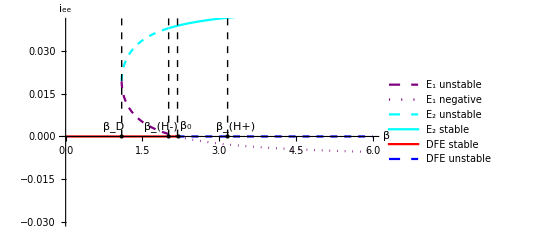

bif1J.pdf

```mathematica
(*Bifurcation analysis with one parameter free (β*)
Print["the numerical instance is ", cncut]

(**Bifurcation Diagram *)

xm=0;ym=-0.03;xM=6;yM=.04;

Print["β0=",b0n=b0//.currentCond//.cncut//N, " ,β_D=", bc1=bD2//.cncut//N, " ,β_(H-)=", bH1n=bH1//.cncut//N,
" ,β_(H+)=", bH2n=bH2//.cncut//N]

lin1=Line[{{ bc1,0},{ bc1,0.5}}];
li1=Graphics[{Thick,Black,Dashed,lin1}];
lin2=Line[{{ bH1n,0},{ bH1n,0.5}}];
li2=Graphics[{Thick,Black,Dashed,lin2}];
lin3=Line[{{ b0n,0},{ b0n,0.5}}];
li3=Graphics[{Thick,Black,Dashed,lin3}];
lin4=Line[{{ bH2n,0},{ bH2n,0.5}}];
li4=Graphics[{Thick,Black,Dashed,lin4}];

pE2a=Plot[{i/.ie2[[2]]}//.cncut,{β,0,bH1n},PlotStyle->{Dashed,Thick,Cyan},PlotRange->All,PlotLegends->{"E_2 unstable"}];
pE2b=Plot[{i/.ie2[[2]]}//.cncut,{β,bH1n,xM},PlotStyle->{Thick,Cyan},PlotRange->All,PlotLegends->{"E_2 stable "}];

pE1a=Plot[{i/.ie2[[1]]}//.cncut,{β,0,b0n},PlotStyle->{Dashed,Thick,Purple},PlotRange->All,PlotLegends->{"E_1 unstable "}];
pE1b=Plot[{i/.ie2[[1]]}//.cncut,{β,b0n,xM},PlotStyle->{Dotted,Thick,Purple},PlotRange->All,PlotLegends->{"E_1 negative "}];



pdfea=Plot[0,{β,0, b0n},PlotStyle->{Thick,Red},PlotRange->All,
PlotLegends->{"DFE stable"}];
pdfeb=Plot[0,{β,b0n, xM},PlotStyle->{Dashed,Thick,Blue},PlotRange->All,
PlotLegends->{"DFE unstable"}];
bif=Show[{ pE1a,pE1b,   pE2a,pE2b,pdfea,pdfeb,li1,li2,li3,li4},PlotRange->{{xm,xM},{ym,yM}},Epilog->
{{Text["β_0",Offset[{8,10},{ b0n,0}]],{PointSize[Large],
Style[Point[{ b0n,0}],Orange]},Text["β_D",Offset[{-8,10},{ bc1,0}]],
{PointSize[Large],Style[Point[{ bc1,0}],Black]},Text["β_(H-)",Offset[{-8,10},{ bH1n,0}]],
{PointSize[Large],Style[Point[{ bH1n,0}],Green]},Text["β_(H+)",Offset[{8,10},{ bH2n,0}]],
{PointSize[Large],Style[Point[{ bH2n,0}],Green]}}
},AxesLabel->{"β","i_ee"},AxesOrigin->{0,0}]

Export["bif1J.pdf",bif]
```

### UP TO HERE!!

#### Some Checks!

Below, we check some results:

```mathematica
Print["βH+ and βH- are >0 iff "]
bHp=Reduce[Join[{bH1>0,bH2>0},cp],γ]//FullSimplify

(*Reduce[bH1>bD]//FullSimplify*)
%//.fip
Print["βH- =",
NumberForm[bH1//.fip//N,10], " and βH+ =", NumberForm[bH2//.fip//N,10], " and βD =", NumberForm[bD//.fip//N,10]]
```

βH+ and βH- are >0 iff

β>0&&γ_s>0&&δ>0&&γ_r>0&&μ>0&&ν>0&&Λ>(4 μ)/ν&&γ≥γ_r+(μ (5 γ_r+4 μ))/(-4 μ+Λ ν)+(2 √(μ/(Λ ν)) (γ_r μ+Λ (γ_r+μ) ν))/(-4 μ+Λ ν)

γ_s>0&&δ>0

βH- =2.013568546 and βH+ =3.166237321 and βD =1.095410811

```mathematica
(*Checks of stability*)
RHScut=RHS//.cncut; 
jacut=Grad[RHScut,{s,i}];
Print["Stability Analysis of E1"]

Print["The eigenvalues  at βD are"]
Chop[Eigenvalues[jacut/.ie2[[1]]/.β->(bD)//.cncut//N],10^(-8)]

Print["The eigenvalues  between βD and βH- are"]
Chop[Eigenvalues[jacut/.ie2[[1]]/.β->(bH1+bD)/2//.cncut//N]]

Print["The eigenvalues  between βH- and β0 are"]
Chop[Eigenvalues[jacut/.ie2[[1]]/.β->(b0n+bH1)/2//.cncut//N]]
Print["The eigenvalues  between βH+ and β0 are"]
Chop[Eigenvalues[jacut/.ie2[[1]]/.β->(b0n+bH2)/2//.cncut//N]]

Print["The eigenvalues  after β0 are"]
Chop[Eigenvalues[jacut/.ie2[[1]]/.β->(b0n)+1/2//.cncut//N]]
Print["The eigenvalues  after βH+ are"]
Chop[Eigenvalues[jacut/.ie2[[1]]/.β->(bH2)+1/2//.cncut//N]]
Print["The eigenvalues    at βH1 "]
Chop[Eigenvalues[jacut/.ie2[[1]]/.β->(bH1)//.cncut//N]]
Print["The eigenvalues    at βH2 "]
Chop[Eigenvalues[jacut/.ie2[[1]]/.β->(bH2)//.cncut//N]]

Print["Stability Analysis of E2"]

Print["The eigenvalues  at βD are"]
Chop[Eigenvalues[jacut/.ie2[[2]]/.β->(bD)//.cncut//N],10^(-8)]

Print["The eigenvalues  between βD and βH+ are"]
Chop[Eigenvalues[jacut/.ie2[[2]]/.β->(bH2+bD)/2//.cncut//N]]
Print["The eigenvalues  between βH+ and βH- are"]
Chop[Eigenvalues[jacut/.ie2[[2]]/.β->(bH2+bH1)/2//.cncut//N]]
Print["The eigenvalues  between βH- and β0 are"]
Chop[Eigenvalues[jacut/.ie2[[2]]/.β->(b0n+bH1)/2//.cncut//N]]

Print["The eigenvalues    at βH1 "]
Chop[Eigenvalues[jacut/.ie2[[2]]/.β->(bH1)//.cncut//N],10^(-8)]
Print["The eigenvalues    at βH2 "]
Chop[Eigenvalues[jacut/.ie2[[2]]/.β->(bH2)//.cncut//N]]
```

Stability Analysis of E1

The eigenvalues  at βD are

{0.596801,0}

The eigenvalues  between βD and βH- are

{0.250696+0.394256 ⅈ,0.250696-0.394256 ⅈ}

The eigenvalues  between βH- and β0 are

{0.167557+0.626044 ⅈ,0.167557-0.626044 ⅈ}

The eigenvalues  between βH+ and β0 are

{0.0773079+0.788327 ⅈ,0.0773079-0.788327 ⅈ}

The eigenvalues  after β0 are

{0.0756331+0.790898 ⅈ,0.0756331-0.790898 ⅈ}

The eigenvalues  after βH+ are

{-0.0792923+0.986692 ⅈ,-0.0792923-0.986692 ⅈ}

The eigenvalues    at βH1

{0.181034+0.596342 ⅈ,0.181034-0.596342 ⅈ}

The eigenvalues    at βH2

{0.+0.895589 ⅈ,0.-0.895589 ⅈ}

Stability Analysis of E2

The eigenvalues  at βD are

{0.596801,0}

The eigenvalues  between βD and βH+ are

{-0.0991986,0.0293713}

The eigenvalues  between βH+ and βH- are

{-0.258356,-0.0835331}

The eigenvalues  between βH- and β0 are

{-0.0974887,0.0456815}

The eigenvalues    at βH1

{-0.0937997,0.0937997}

The eigenvalues    at βH2

{-0.590244,-0.0916103}

```mathematica
(*Below, we check numerically that E2 is always unstable before β0*)
eig1=Eigenvalues[jaci2//.ie2[[2]]];
Reduce[Join[Thread[(i//.ie2)>0]//.cncut,Thread[eig1<0]//.cncut,cp],β]
Reduce[Join[Thread[(i//.ie2)>0]//.cncut,{eig1[[1]]>0//.cncut,eig1[[2]]<0//.cncut},cp],β]
Reduce[Join[Thread[(i//.ie2)>0]//.cncut,{eig1[[1]]<0//.cncut,eig1[[2]]>0//.cncut},cp],β]//N
```

False

False

γ>0.&&γ_r>0.&&γ_s>0.&&δ>0.&&Λ>0.&&μ>0.&&ν>0.&&1.09541<β<2.1875

```mathematica
cut=Drop[cncut,-1];
Chop[Eigenvalues[jacD/.ie2[[1]]//.ν->nuc//.cut//N],10^(-8)]
Print["the system admits a BT points iff "]
Timing[cBT1=Reduce[Join[{tr1==0,det1==0}//.cncut,cp]]]
Print["the system admits a BT points iff "]
Timing[cBT1=Reduce[Join[{tr1==0,det1==0}//.ν->nuc//.cut,cp]]]
%//N
```

{0,0}

the system admits a BT points iff

{0.015625,False}

the system admits a BT points iff

{0.03125,β==16262331075/7516192768&&γ>0&&γ_r>0&&γ_s>0&&δ>0&&Λ>0&&μ>0&&ν>0}

{0.03125,β==2.16364&&γ>0.&&γ_r>0.&&γ_s>0.&&δ>0.&&Λ>0.&&μ>0.&&ν>0.}